```mathematica
Show[
ParametricPlot3D[{{t,1-t,0},{t,0,0},{0,t,0}},{t,0,1},PlotStyle->Red,Boxed->False,Axes->None,PlotRange->{{0,1.4},{0,1.4},{0,1.4}}],
Graphics3D[Line[{{1,0,0},{1.2,0,0}}]],
Graphics3D[Line[{{0,1,0},{0,1.2,0}}]],
Graphics3D[Line[{{0,0,0},{0,0,1.2}}]]
]
```

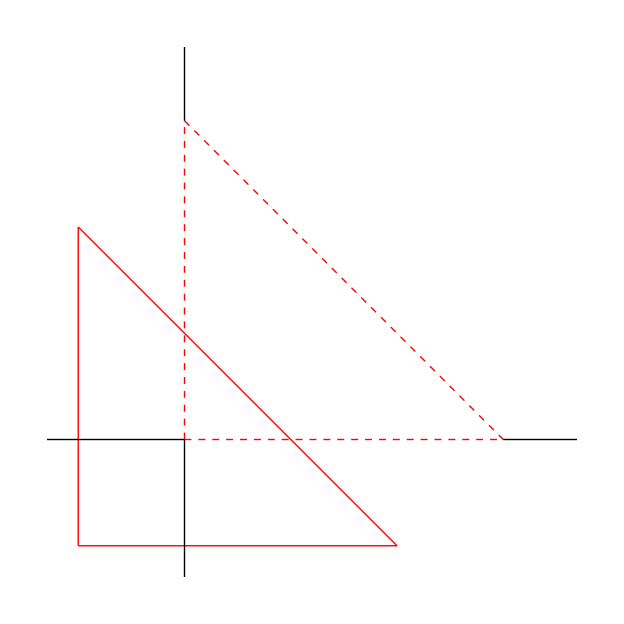

```mathematica
Show[
ParametricPlot[{{t,1-t},{0,t},{t,0}},{t,0,1}, PlotStyle->{{Dashed,Red},{Dashed,Red},{Dashed,Red}},Axes->None,PlotRange->{{-.4,1.2},{-.4,1.2}}],
ParametricPlot[{{t-1/3,1-t-1/3},{-1/3,t-1/3},{t-1/3,-1/3}},{t,0,1}, PlotStyle->Red],
Graphics[Line[{{-1.5,0},{0,0}}]],
Graphics[Line[{{1.5,0},{1,0}}]],
Graphics[Line[{{0,-1.5},{0,0}}]],
Graphics[Line[{{0,1.5},{0,1}}]]
]
```

```mathematica
Show[
ParametricPlot[{{t-1/3,1-t-1/3},{-1/3,t-1/3},{t-1/3,-1/3}},{t,0,1}, PlotStyle->{{Dashed,Red},{Dashed,Red},{Dashed,Red}},Axes->None,PlotRange->{{-1.2,1.2},{-1.2,1.2}}],
Table[Graphics[{Thin,Arrowheads->Small,Red,Arrow[{(0.02){Cos[t],Sin[t]},(0.95){Cos[t],Sin[t]}}]}],{t,0,2π,(2π)/11}],
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}],
Graphics[Line[{{-1.2,0},{-0.02,0}}]],
Graphics[Line[{{0.02,0},{1.2,0}}]],
Graphics[Line[{{0,-1.2},{0,-0.02}}]],
Graphics[Line[{{0,0.02},{0,1.2}}]]
]
```